# Hard unknots (ExternalEvaluator)

--Jason, August 2024. The purpose of this notebook is to experiment with using the new ExternalEvaluator functionality in 14.1 to establish a Python environment which contains snappy, and then to use that environment to construct hard unknots from Burton’s paper using the Gauss code to PD code functions in snappy.

```mathematica
Exit
```

## Defining the hard unknots.

```mathematica
PicD28 = {-Graphics-};
```

```mathematica
GaussD28 ="1 -4 -3 6 5 -2 -7 8 4 -5 -9 10 2 -1 -11 7 12 -13 -6 3 14 -12 -10 9 13 -14 -8 11 15 -18 -17 20 19 -16 -21 17 22 -23 -20 21 24 -15 -25 26 16 -19 -27 28 18 -24 -26 27 23 -22 -28 25";
```

```mathematica
PicD43= {-Graphics-};
```

```mathematica
GaussD43 = "-1 2 -3 -4 -5 6 -7 8 -9 10 -11 12 -13 3 14 -15 16 -17 18 -19 20 1 -21 22 -23 24 -25 7 -26 27 -10 28 -29 13 4 30 31 -32 17 -33 34 35 -2 -36 -22 -37 -38 25 -8 39 -27 11 -40 29 41 23 37 -31 42 -16 33 -43 19 -20 -35 -14 -30 5 -6 38 -24 9 -39 26 -12 40 -28 -41 36 21 32 -42 15 -34 43 -18";
```

```mathematica
PicD78 = {-Graphics-};
```

```mathematica
GaussD78 = " 1 2 -3 -4 5 6 -7 -8 9 10 -2 -11 12 13 -14 -5 15 16 17 18 -19 -20 21 22 -6 -23 24 25 -26 -1 27 28 -29 -30 23 14 -31 -32 11 26 -33 -34 30 7 -22 -15 4 31 -13 -24 34 36 -28 -9 20 -17 37 38 35 39 -40 41 42 -43 -44 45 46 -47 -48 49 -39 -50 51 -52 -53 54 43 -55 -56 48 57 -58 -38 -61 -59 60 52 -62 -41 56 63 -46 -64 65 58 -66 -49 40 67 -51 -68 59 69 -70 -45 71 55 -42 -72 53 74 -69 -73 -37 -65 75 47 -63 -71 44 76 -74 -60 68 -77 -35 66 -57 -75 64 70 -76 -54 72 62 -67 50 77 61 73 -18 19 -10 -27 78 33 -25 -12 32 3 -16 -21 8 29 -36 -78";
```

```mathematica
PicH ={-Graphics-};
```

```mathematica
GaussH = "-1 2 -3 4 -5 -6 7 -8 9 1 -2 3 -4 -9 6 -7 8 5";
```

```mathematica
PicJ = {-Graphics-};
```

```mathematica
GaussJ = "-1 2 -3 4 5 -6 7 1 -4 3 -2 -5 8 -9 6 -7 9 -8";
```

```mathematica
PicCulprit = {-Graphics-};
```

```mathematica
GaussCulprit = " -1 2 -3 4 -5 6 7 8 -9 10 -4 5 -6 3 -2 -7 -10 1 -8 9";
```

```mathematica
PicMonster = {-Graphics-};
```

```mathematica
GaussMonster = "1 -2 3 4 5 -6 7 -8 9 -3 10 -1 2 -10 -4 -9 8 -5 6 -7";
```

```mathematica
PicGoeritz = {-Graphics-};
```

```mathematica
GaussGoeritz = "1 -2 3 -4 -5 6 -7 8 -9 -10 11 -1 2 -3 4 -11 10 7 -8 9 -6 5";
```

```mathematica
PicThistlethwaite = {-Graphics-};
```

```mathematica
GaussThistlethwaite = "1 2 -3 4 5 -6 -7 8 -9 10 -11 -5 12 -1 6 13 -10 -14 -4 15 -2 9 -8 7 -13 11 14 3 -15 -12";
```

```mathematica
PicOchai ={-Graphics-};
```

```mathematica
GaussOchai ="-1 2 3 -4 -5 -6 -7 8 -9 10 -11 -3 4 -12 13 14 -8 7 -14 -15 12 5 -2 1 -16 11 -10 9 15 -13 6 16";
```

```mathematica
PicTuzunSikora ={-Graphics-};
```

```mathematica
GaussTuzunSikora = "1 6 -7 10 11 12 -14 -15 16 -17 -18 -2 3 -4 5 7 -9 -11 17 -21 19 -20 -8 9 -10 18 21 -16 -13 14 20 -1 2 -3 4 -5 -6 8 -12 13 15 -19";
```

```mathematica
PicGaussFakeFHW ={-Graphics-};
```

```mathematica
GaussFakeFHW = "1 -2 -3 -4 5 6 -7 -8 4 9 -10 -5 8 11 2 12 -13 -1 14 7 -6 -15 16 3 -11 -14 15 10 -9 -16 -12 13 17 -18 -19 -20 21 22 -23 -24 25 19 -22 -26 27 23 -28 -17 18 29 24 30 -31 -21 20 32 -30 -27 26 31 -32 -25 -29 28";
```

```mathematica
PicFHW = {-Graphics-};
```

```mathematica
GaussFHW= "3 4 -5 -8 10 12 -13 -15 8 7 -9 -10 15 16 -4 1 17 -20 32 31 -27 -25 22 24 -31 -29 28 27 -24 -23 20 19 -18 -17 -21 -22 25 26 -30 -32 23 21 -26 -28 29 30 -19 18 2 -3 14 13 -12 -11 6 5 -16 -14 11 9 -7 -6 -1 -2";
```

```mathematica
PicOchaiII = {-Graphics-};
```

```mathematica
GaussOchaiII = " -1 2 -3 -4 5 -6 -7 8 -9 10 -11 -12 13 -14 15 16 4 -17 6 18 -19 11 20 21 -22 -23 24 25 -26 27 -28 29 14 30 -31 -13 -25 32 -33 -34 -27 28 35 36 -37 22 38 -39 12 -40 -41 42 -16 3 -2 1 -21 -38 23 37 45 -35 34 26 -29 -15 -42 43 -18 9 -8 7 17 -5 -43 41 -44 31 -30 44 40 19 -10 -20 39 -24 -32 33 -36 -45";
```

```mathematica
PicReducedOchaiII = {-Graphics-};
```

```mathematica
GaussReducedOchaiII = "1 -2 -21 -3 4 -6 -5 7 -8 -10 9 -11 12 15 -13 14 3 5 -16 17 -18 19 10 21 22 13 23 -24 20 -12 25 -26 -27 28 -30 31 29 -32 11 -20 -15 33 2 -1 -31 30 -28 27 -33 -22 -14 34 -17 8 -7 16 6 -4 -34 -35 24 -23 35 18 -19 -9 32 -25 26 -29";
```

```mathematica
PicOchaiIII ={-Graphics-};
```

```mathematica
GaussOchaiIII="1 3 31 30 -45 -44 65 64 62 63 -56 -57 54 55 -3 -4 7 8 -10 -9 24 23 49 48 -67 -65 -42 -43 33 32 -38 -39 40 42 44 46 -48 -50 17 18 -13 -15 -52 -54 57 58 -61 -62 39 37 -34 -33 -30 -29 -27 26 -25 -24 -22 -19 -18 13 14 11 9 -7 -5 2 4 28 29 -47 -46 67 66 61 60 -59 -58 52 53 -1 -2 5 6 -12 -11 22 21 51 50 -66 -64 -40 -41 34 35 -36 -37 41 43 45 47 -49 -51 20 19 -14 -16 -53 -55 56 59 -60 -63 38 36 -35 -32 -31 -28 27 -26 25 -23 -21 -20 -17 15 16 12 10 -8 -6";
```

```mathematica
PicOchaiIV = {-Graphics-};
```

```mathematica
GaussOchaiIV = "1 -2 3 6 7 -8 9 -10 -11 12 8 -9 10 13 -14 -15 16 -17 -19 20 15 -16 17 -21 22 23 -24 14 25 26 27 -28 -29 -30 -13 -31 32 -33 -23 24 31 -32 33 34 -35 19 -20 -25 30 11 -12 36 37 4 -5 38 39 -40 41 29 -26 -42 43 -44 -45 46 42 -43 44 -47 -38 -48 49 -50 -51 52 48 -49 50 -37 -6 35 21 -22 -34 -7 -36 51 -52 -39 -53 45 -46 -27 28 54 -55 18 40 -41 -54 55 -18 53 47 -1 2 -3 -4 5";
```

```mathematica
PicHaken={-Graphics-};
```

```mathematica
GaussHaken = "-1 -2 3 -4 5 6 7 8 -9 -10 11 12 13 -14 15 -16 17 18 -19 20 -21 -7 22 23 24 -25 -26 -27 28 -29 30 31 -32 -33 -34 35 36 -37 -38 -39 -40 -41 42 43 -44 45 46 47 -48 -49 -50 38 -51 52 -53 -54 -55 -42 -56 57 58 -46 -59 -60 -61 -62 63 -64 -65 -66 -67 68 -35 -69 70 -71 -72 73 29 -74 -31 -75 -76 77 69 -36 -68 -78 -79 -80 64 -63 -81 -82 60 -83 -47 84 -57 -85 -43 55 -86 -87 -52 -88 37 -89 49 -90 -84 -58 -45 44 85 56 -91 -92 39 51 88 -70 -77 -93 33 -94 74 -30 -73 95 27 -96 -97 98 -23 99 -8 21 100 -101 -18 102 -103 -15 -104 105 -12 106 -107 9 -99 -22 108 -5 -109 110 2 -111 -112 113 -114 -28 -95 72 115 -116 75 32 94 117 78 -118 66 -119 120 121 83 59 10 107 -122 -123 124 103 16 125 -110 -3 126 127 -98 -24 54 86 -128 40 92 129 90 48 -121 -130 62 81 -131 104 14 132 -133 -124 -134 19 101 135 -6 -108 -127 136 137 114 -113 -138 139 -126 4 109 -135 -100 -20 140 123 133 -132 -13 -105 131 141 79 118 67 89 50 -129 91 41 128 87 53 25 97 -136 -139 111 1 -125 -17 -102 134 -140 122 -106 -11 82 61 130 -120 119 65 80 -141 -117 34 93 76 116 -115 71 26 96 -137 138 112";
```

```mathematica
PicPZ31 = {-Graphics-};
```

```mathematica
GaussPZ31 ="2 -3 4 -19 16 -21 -22 1 -20 26 -27 -29 21 -16 -17 7 -8 -13 -26 -25 28 27 14 -15 29 30 -31 -28 25 -24 23 31 -30 22 19 -18 6 9 11 -12 13 -14 15 17 18 5 -9 10 12 20 24 -23 -1 -2 3 -4 -5 -6 -7 8 -10 -11";
```

```mathematica
PicPZ120={-Graphics-};
```

```mathematica
GaussPZ120 = "1 2 -120 -117 -116 -115 114 113 -112 -111 -110 32 -31 -30 29 40 -39 -38 37 78 77 -92 91 90 -89 88 87 68 -66 64 53 -51 48 45 -43 -41 38 34 -33 -37 41 42 -40 -36 35 39 -42 -44 46 49 -52 54 65 -67 69 116 108 99 -101 103 111 50 -49 -48 51 52 -50 -47 44 43 -45 -46 47 110 102 -100 98 12 11 80 -85 -91 92 86 -80 -79 83 89 -90 -84 79 9 10 -93 95 -98 100 101 -99 96 -94 97 -96 -95 93 94 -97 109 117 -74 71 -69 67 66 -68 70 -73 72 -70 -71 74 73 -72 81 82 -83 84 85 -86 75 76 33 -34 -35 36 25 -26 -27 28 -102 -103 -104 105 106 -107 -108 -109 6 -8 -10 -12 -14 17 20 -22 -24 27 31 -32 -28 24 23 -25 -29 30 26 -23 -21 19 16 -13 -11 -9 -7 5 -82 -88 57 -55 -77 -75 15 -16 -17 14 13 -15 -18 21 22 -20 -19 18 -76 -78 -56 58 -53 -54 118 -113 -105 104 112 -118 -119 115 107 -106 -114 119 -65 -64 -63 60 -58 56 55 -57 59 -62 61 -59 -60 63 62 -61 -87 -81 -1 3 -5 7 8 -6 4 -2 120 -4 -3";
```

```mathematica
PicPZ138 = {-Graphics-};
```

```mathematica
GaussPZ138=StringReplace[" 1 -11 -12 -13 -14 34
-46 -58 70 -86 -98 -110 -122 126 -130 -134 138 -111
-99 -87 -75 27 -28 -29 30 -31 -32 -33 -34 35 -36 -37
38 -138 -137 -136 -135 115 -103 -91 79 -63 -51 -39 -27
23 -19 -15 11 -38 -50 -62 -74 122 -121 -120 119 -118
-117 -116 -115 114 -113 -112 111 -1 2 -3 8 99 -100
-101 102 103 104 105 106 107 -108 -109 110 73 61 49 37
12 -16 -20 24 28 40 52 64 80 -92 -104 116 131 132 133
134 50 -49 -48 47 46 45 44 43 42 -41 -40 39 76 88 100
112 137 -133 -129 125 121 109 97 85 69 -57 -45 33 18
17 16 15 6 -4 -2 3 5 7 19 20 21 22 32 -44 -56 68 84 96
108 120 124 -128 -132 136 113 101 89 77 51 -52 -53 54
55 56 57 58 59 -60 -61 62 130 129 128 127 117 -105 -93
81 65 53 41 29 25 -21 -17 13 36 48 60 72 98 -97 -96 95
94 93 92 91 90 -89 -88 87 9 -5 4 -6 -7 -10 75 -76 -77
78 -79 -80 -81 -82 83 -84 -85 86 -71 -59 -47 -35 14
-18 -22 26 -30 -42 -54 -66 82 -94 -106 118 -123 -124
-125 -126 74 -73 -72 71 -70 -69 -68 -67 66 -65 -64 63
-78 -90 -102 -114 135 -131 -127 123 -119 -107 -95 -83
67 -55 -43 31 -26 -25 -24 -23 10 -9 -8","\n"->" "];
```

Now we assemble all of this into a new Association:

```mathematica
MakeDiagramRecord[name_]:= name-><|"GaussCode"->ToExpression["Gauss"<>name],"Diagram"->ToExpression["Pic"<>name],"Name"->name|>;
```

```mathematica
HardUnknotsInitial = <|MakeDiagramRecord /@ {"D28","D43","D78","H","J","Culprit","Monster","Goeritz","Thistlethwaite","Ochai","TuzunSikora","FakeFHW","FHW","OchaiII","ReducedOchaiII","OchaiIII","OchaiIV","Haken","PZ31","PZ120","PZ138"}|>;
```

## Using Regina to add crossing signs and pdcodes

Now we need to create a Regina session to interface with:

```mathematica
regina=StartExternalSession[{"Python","Evaluator"-><|"Dependencies"->{"regina"},"EnvironmentName"->"reginaenv"|>}]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[regina,"import regina; print(regina.Link.fromGauss(\"1 -2 3 -1 2 -3\"))"]
```

3-crossing knot: +++ ( ^0 _1 ^2 _0 ^1 _2 )

Now we can actually run through Regina

```mathematica
ClearAll[ConvertToPD];ConvertToPD[gauss_]:= 
Map[#-1&,List@@(List@@@ToExpression[
ExternalEvaluate[regina,
"regina.Link.fromGauss(\""<>gauss<>"\").pd()"
]]
),{2}]
```

The CrossingSigns function is commented out because the numbering on the signs don’t seem to correspond to order in which crossings appear in the PD code.

```mathematica
PDCodeAppendSign=Compile[{{X,_Integer,1}},Module[{i,j,k,l},i=Compile`GetElement[X,1];
j=Compile`GetElement[X,2];
k=Compile`GetElement[X,3];
l=Compile`GetElement[X,4];
If[(i==j)||(k==l)||(j-l==1)||(l-j>1),{i,j,k,l,1},If[(i==l)||(j==k)||(l-j==1)||(j-l>1),{i,j,k,l,-1},{i,j,k,l,0}]]],CompilationTarget->"C",RuntimeAttributes->{Listable}];
```

```mathematica
(*ClearAll[CrossingSigns];CrossingSigns[gauss_]:= 
Transpose[{ExternalEvaluate[regina,
"[[cr.sign(),cr.index()] for cr in regina.Link.fromGauss(\""<>gauss<>"\").crossings()]"
]}]*)
```

```mathematica
PDCodeAppendSign @ ConvertToPD[GaussD28]
```

{{0,8,1,7,1},{1,18,2,19,-1},{4,12,5,11,1},{5,14,6,15,-1},{8,4,9,3,1},{9,22,10,23,-1},{12,0,13,55,1},{13,26,14,27,-1},{16,24,17,23,1},{17,2,18,3,-1},{20,16,21,15,1},{21,10,22,11,-1},{24,20,25,19,1},{25,6,26,7,-1},{28,48,29,47,1},{29,34,30,35,-1},{32,44,33,43,1},{33,38,34,39,-1},{36,52,37,51,1},{37,30,38,31,-1},{40,28,41,27,1},{41,54,42,55,-1},{44,32,45,31,1},{45,50,46,51,-1},{48,40,49,39,1},{49,42,50,43,-1},{52,36,53,35,1},{53,46,54,47,-1}}

```mathematica
HardUnknots = <|Append[#,{"PDcode"->ConvertToPD[#["GaussCode"]]}]& /@ HardUnknotsInitial|>;
```

Now let’s test that this actually worked in a particular case.

```mathematica
HardUnknots["D28"]
```

<|GaussCode→1 -4 -3 6 5 -2 -7 8 4 -5 -9 10 2 -1 -11 7 12 -13 -6 3 14 -12 -10 9 13 -14 -8 11 15 -18 -17 20 19 -16 -21 17 22 -23 -20 21 24 -15 -25 26 16 -19 -27 28 18 -24 -26 27 23 -22 -28 25,Diagram→{-Graphics-},Name→D28,PDcode→{{0,8,1,7},{1,18,2,19},{4,12,5,11},{5,14,6,15},{8,4,9,3},{9,22,10,23},{12,0,13,55},{13,26,14,27},{16,24,17,23},{17,2,18,3},{20,16,21,15},{21,10,22,11},{24,20,25,19},{25,6,26,7},{28,48,29,47},{29,34,30,35},{32,44,33,43},{33,38,34,39},{36,52,37,51},{37,30,38,31},{40,28,41,27},{41,54,42,55},{44,32,45,31},{45,50,46,51},{48,40,49,39},{49,42,50,43},{52,36,53,35},{53,46,54,47}}|>

Finally, we’ll output these to various files in the right place:

```mathematica
(*Export[NotebookDirectory[]<>"../data/diagrams/hardunknots/"<>#["Name"]<>".tsv",PDCodeAppendSign[#["PDcode"]]]& /@ HardUnknots*)
```

If we want to kill the external session, we can use:

```mathematica
DeleteObject[regina]
```

## Hard unknots of Juhasz et al.

We can load their original “very-hard-unknots.csv” directly:

```mathematica
JuhaszUnknots = Import[NotebookDirectory[]<>"very_hard_unknots.csv"];
```

```mathematica
ConvertedToLists = First[(ToExpression@StringReplace[#,{"["->"{","]"->"}"}])]& /@JuhaszUnknots[[2;;]];
```

```mathematica
JuhaszUnknotRecords = Table[<|"PDcode"->Map[#-1&,ConvertedToLists[[i+1]],{2}],"Name"->"juhasz-veryhard-"<>ToString[i]|>,{i,1,Length[ConvertedToLists]-1}];
```

```mathematica
(*Export[Echo[NotebookDirectory[]<>"../data/diagrams/veryhardunknots/"<>#["Name"]<>".tsv"],PDCodeAppendSign[#["PDcode"]]]& /@ JuhaszUnknotRecords*)
```

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-1.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-2.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-3.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-4.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-5.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-6.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-7.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-8.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-9.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-10.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-11.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-12.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-13.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-14.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-15.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-16.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-17.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-18.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-19.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-20.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-21.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-22.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-23.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-24.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-25.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-26.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-27.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-28.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-29.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-30.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-31.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-32.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-33.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-34.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-35.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-36.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-37.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-38.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-39.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-40.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-41.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-42.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-43.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-44.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-45.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-46.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-47.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-48.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-49.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-50.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-51.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-52.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-53.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-54.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-55.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-56.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-57.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-58.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-59.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-60.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-61.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-62.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-63.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-64.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-65.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-66.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-67.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-68.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-69.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-70.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-71.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-72.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-73.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-74.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-75.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-76.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-77.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-78.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-79.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-80.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-81.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-82.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-83.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-84.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-85.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-86.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-87.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-88.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-89.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-90.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-91.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-92.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-93.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-94.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-95.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-96.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-97.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-98.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-99.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-100.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-101.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-102.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-103.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-104.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-105.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-106.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-107.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-108.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-109.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-110.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-111.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-112.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-113.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-114.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-115.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-116.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-117.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-118.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-119.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-120.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-121.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-122.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-123.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-124.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-125.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-126.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-127.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-128.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-129.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-130.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-131.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-132.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-133.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-134.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-135.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-136.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-137.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-138.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-139.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-140.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-141.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-142.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-143.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-144.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-145.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-146.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-147.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-148.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-149.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-150.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-151.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-152.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-153.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-154.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-155.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-156.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-157.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-158.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-159.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-160.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-161.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-162.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-163.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-164.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-165.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-166.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-167.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-168.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-169.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-170.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-171.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-172.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-173.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-174.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-175.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-176.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-177.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-178.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-179.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-180.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-181.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-182.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-183.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-184.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-185.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-186.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-187.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-188.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-189.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-190.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-191.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-192.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-193.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-194.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-195.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-196.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-197.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-198.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-199.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-200.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-201.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-202.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-203.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-204.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-205.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-206.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-207.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-208.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-209.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-210.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-211.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-212.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-213.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-214.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-215.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-216.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-217.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-218.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-219.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-220.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-221.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-222.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-223.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-224.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-225.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-226.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-227.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-228.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-229.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-230.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-231.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-232.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-233.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-234.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-235.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-236.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-237.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-238.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-239.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-240.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-241.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-242.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-243.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-244.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-245.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-246.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-247.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-248.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-249.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-250.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-251.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-252.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-253.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-254.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-255.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-256.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-257.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-258.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-259.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-260.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-261.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-262.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-263.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-264.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-265.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-266.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-267.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-268.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-269.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-270.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-271.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-272.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-273.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-274.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-275.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-276.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-277.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-278.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-279.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-280.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-281.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-282.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-283.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-284.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-285.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-286.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-287.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-288.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-289.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-290.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-291.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-292.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-293.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-294.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-295.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-296.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-297.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-298.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-299.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-300.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-301.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-302.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-303.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-304.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-305.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-306.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-307.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-308.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-309.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-310.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-311.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-312.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-313.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-314.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-315.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-316.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-317.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-318.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-319.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-320.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-321.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-322.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-323.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-324.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-325.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-326.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-327.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-328.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-329.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-330.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-331.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-332.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-333.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-334.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-335.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-336.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-337.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-338.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-339.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-340.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-341.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-342.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-343.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-344.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-345.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-346.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-347.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-348.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-349.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-350.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-351.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-352.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-353.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-354.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-355.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-356.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-357.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-358.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-359.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-360.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-361.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-362.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-363.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-364.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-365.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-366.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-367.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-368.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-369.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-370.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-371.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-372.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-373.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-374.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-375.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-376.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-377.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-378.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-379.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-380.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-381.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-382.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-383.tsv

/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-384.tsv

{/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-1.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-2.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-3.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-4.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-5.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-6.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-7.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-8.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-9.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-10.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-11.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-12.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-13.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-14.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-15.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-16.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-17.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-18.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-19.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-20.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-21.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-22.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-23.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-24.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-25.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-26.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-27.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-28.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-29.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-30.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-31.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-32.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-33.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-34.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-35.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-36.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-37.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-38.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-39.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-40.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-41.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-42.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-43.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-44.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-45.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-46.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-47.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-48.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-49.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-50.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-51.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-52.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-53.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-54.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-55.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-56.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-57.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-58.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-59.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-60.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-61.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-62.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-63.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-64.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-65.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-66.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-67.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-68.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-69.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-70.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-71.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-72.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-73.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-74.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-75.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-76.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-77.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-78.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-79.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-80.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-81.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-82.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-83.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-84.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-85.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-86.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-87.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-88.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-89.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-90.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-91.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-92.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-93.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-94.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-95.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-96.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-97.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-98.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-99.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-100.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-101.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-102.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-103.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-104.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-105.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-106.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-107.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-108.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-109.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-110.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-111.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-112.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-113.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-114.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-115.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-116.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-117.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-118.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-119.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-120.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-121.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-122.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-123.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-124.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-125.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-126.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-127.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-128.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-129.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-130.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-131.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-132.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-133.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-134.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-135.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-136.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-137.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-138.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-139.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-140.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-141.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-142.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-143.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-144.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-145.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-146.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-147.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-148.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-149.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-150.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-151.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-152.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-153.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-154.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-155.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-156.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-157.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-158.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-159.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-160.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-161.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-162.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-163.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-164.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-165.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-166.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-167.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-168.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-169.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-170.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-171.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-172.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-173.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-174.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-175.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-176.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-177.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-178.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-179.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-180.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-181.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-182.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-183.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-184.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-185.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-186.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-187.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-188.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-189.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-190.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-191.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-192.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-193.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-194.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-195.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-196.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-197.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-198.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-199.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-200.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-201.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-202.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-203.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-204.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-205.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-206.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-207.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-208.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-209.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-210.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-211.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-212.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-213.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-214.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-215.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-216.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-217.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-218.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-219.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-220.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-221.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-222.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-223.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-224.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-225.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-226.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-227.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-228.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-229.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-230.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-231.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-232.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-233.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-234.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-235.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-236.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-237.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-238.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-239.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-240.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-241.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-242.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-243.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-244.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-245.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-246.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-247.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-248.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-249.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-250.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-251.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-252.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-253.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-254.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-255.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-256.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-257.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-258.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-259.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-260.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-261.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-262.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-263.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-264.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-265.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-266.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-267.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-268.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-269.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-270.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-271.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-272.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-273.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-274.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-275.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-276.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-277.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-278.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-279.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-280.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-281.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-282.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-283.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-284.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-285.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-286.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-287.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-288.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-289.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-290.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-291.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-292.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-293.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-294.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-295.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-296.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-297.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-298.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-299.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-300.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-301.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-302.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-303.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-304.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-305.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-306.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-307.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-308.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-309.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-310.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-311.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-312.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-313.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-314.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-315.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-316.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-317.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-318.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-319.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-320.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-321.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-322.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-323.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-324.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-325.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-326.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-327.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-328.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-329.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-330.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-331.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-332.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-333.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-334.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-335.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-336.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-337.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-338.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-339.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-340.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-341.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-342.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-343.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-344.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-345.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-346.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-347.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-348.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-349.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-350.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-351.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-352.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-353.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-354.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-355.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-356.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-357.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-358.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-359.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-360.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-361.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-362.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-363.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-364.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-365.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-366.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-367.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-368.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-369.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-370.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-371.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-372.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-373.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-374.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-375.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-376.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-377.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-378.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-379.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-380.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-381.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-382.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-383.tsv,/Users/jasoncantarella/KnotTools/Mathematica/../data/diagrams/veryhardunknots/juhasz-veryhard-384.tsv}

## The “children’s game” picture-only knots of Gukov...

We’re going to have to try to parse the svg to construct geometry for these knots (thanks, assholes!). But, ok, this should be a pretty fun bit of hackery. First off, an SVG file is really just an xml file, where we want the Line, Polyline, and Path elements.

```mathematica
Exit[]
```

```mathematica
gukovFilenames = FileNames[FileNameJoin[{NotebookDirectory[],"knotagain","*.svg"}]];
```

```mathematica
target = Import[gukovFilenames[[1]]]
```

-Graphics-

```mathematica
x = Import[gukovFilenames[[1]],"xml"];
```

We now split into “path” and “line” elements; in a “path” element, we generally start with an “M” (moveto) and then have some number of “c” (cubic Bezier spline) elements and “s” (smooth cubic Bezier spline) commands. According to the docs, the cubic spline elements end up at the third point in the triple (which is expressed relative to the original “moveto” point) and the “smooth cubics” end up at the second (which is relative to the end of the previous curve). So this unpleasant block extracts the “M”, “c”, and “s” elements by string pattern matching, takes the endpoints of “c” and “s” elements (by position), and produces a line with goes from the beginning to the end.

```mathematica
Import[gukovFilenames[[1]],"Text"]
```

<?xml version="1.0" encoding="utf-8"?>
<!-- Generator: Adobe Illustrator 28.1.0, SVG Export Plug-In . SVG Version: 6.00 Build 0)  -->
<svg version="1.1" id="Layer_1" xmlns="http://www.w3.org/2000/svg" xmlns:xlink="http://www.w3.org/1999/xlink" x="0px" y="0px"
	 viewBox="0 0 178.89 180" style="enable-background:new 0 0 178.89 180;" xml:space="preserve">
<style type="text/css">
	.st0{fill:none;stroke:#000000;stroke-width:0.5;stroke-linecap:square;stroke-linejoin:round;stroke-miterlimit:10;}
	.st1{fill:none;stroke:#000000;stroke-width:0.5;stroke-miterlimit:10;}
</style>
<g>
	<path class="st1" d="M63.64,106.24c0,15.29,6.11,22.93,18.34,22.93"/>
	<path class="st1" d="M59.05,83.31c-18.34,0-18.34-22.93,0-22.93"/>
	<path class="st1" d="M86.57,78.72c0-12.23-7.64-18.34-22.93-18.34"/>
	<path class="st1" d="M132.42,83.31c15.29,0,22.93,7.64,22.93,22.93"/>
	<path class="st1" d="M155.35,129.17c0,15.29-7.64,22.93-22.93,22.93c-15.29,0-22.93-7.64-22.93-22.93"/>
	<path class="st1" d="M86.57,129.17c0,15.29-7.64,22.93-22.93,22.93"/>
	<path class="st1" d="M40.71,152.09c-15.29,0-22.93-7.64-22.93-22.93"/>
	<path class="st1" d="M17.78,60.38c0-15.29,7.64-22.93,22.93-22.93c15.29,0,22.93,6.11,22.93,18.34"/>
	<path class="st1" d="M109.5,129.17c0-22.93,22.93,0,4.59,0"/>
	<line class="st0" x1="68.22" y1="83.31" x2="86.57" y2="83.31"/>
	<line class="st0" x1="63.64" y1="83.31" x2="63.64" y2="106.24"/>
	<line class="st0" x1="81.98" y1="129.17" x2="81.98" y2="129.17"/>
	<line class="st0" x1="59.05" y1="60.38" x2="63.64" y2="60.38"/>
	<line class="st0" x1="63.64" y1="83.31" x2="63.64" y2="64.96"/>
	<line class="st0" x1="63.64" y1="60.38" x2="63.64" y2="60.38"/>
	<line class="st0" x1="86.57" y1="83.31" x2="132.42" y2="83.31"/>
	<line class="st0" x1="155.35" y1="106.24" x2="155.35" y2="129.17"/>
	<line class="st0" x1="132.42" y1="152.09" x2="132.42" y2="152.09"/>
	<line class="st0" x1="109.5" y1="129.17" x2="109.5" y2="129.17"/>
	<line class="st0" x1="86.57" y1="87.89" x2="86.57" y2="129.17"/>
	<line class="st0" x1="91.15" y1="129.17" x2="104.91" y2="129.17"/>
	<line class="st0" x1="63.64" y1="152.09" x2="40.71" y2="152.09"/>
	<line class="st0" x1="17.78" y1="129.17" x2="17.78" y2="60.38"/>
	<g>
		<line class="st0" x1="40.71" y1="37.45" x2="40.71" y2="37.45"/>
	</g>
	<line class="st0" x1="63.64" y1="55.79" x2="63.64" y2="55.79"/>
	<line class="st0" x1="114.08" y1="129.17" x2="114.08" y2="129.17"/>
</g>
</svg>

```mathematica
PathData[xml_]:=Block[{raw},
raw = GroupBy[First->Last]@Flatten[StringCases[#,
{Shortest["M"~~x__~~LetterCharacter]:>({{"start",ToExpression["{"<>StringReplace[x,Shortest[y:DigitCharacter~~"-"~~z:DigitCharacter]:>(y<>",-"<>z)]<>"}"]}}),Shortest["c"~~x__~~(LetterCharacter|EndOfString|WhitespaceCharacter)]:> 
Block[{bf},
bf = BezierFunction[
Prepend[Partition[
ToExpression["{"<>StringReplace[x,Shortest[y:DigitCharacter~~"-"~~z:DigitCharacter]:>(y<>",-"<>z)]<>"}"],2],{0.,0.}]];Table[{"step",
bf[u]-bf[u-1/7]},{u,1/7,1,1/7}]],
Shortest["s"~~x__~~(LetterCharacter|EndOfString|WhitespaceCharacter)]:> ({{"step",ToExpression["{"<>StringReplace[x,Shortest[y:DigitCharacter~~"-"~~z:DigitCharacter]:>(y<>",-"<>z)]<>"}"][[3;;4]]}})},Overlaps->True],1]&/@ ("d"/.Extract[xml,Position[xml,XMLElement["path",__]]][[All,2]]);
Function[{c},Line[Prepend[(First[c["start"]]+#& /@ Accumulate[c["step"]]),First[c["start"]]]]]/@raw
]
```

```mathematica
PathData[x]
```

{Line[{{63.64,106.24},{64.0141,112.325},{65.1366,117.472},{67.0075,121.684},{69.6272,124.959},{72.9957,127.299},{77.1132,128.702},{81.98,129.17}}],Line[{{59.05,83.31},{52.3129,82.0398},{47.8214,78.7641},{45.5757,74.2851},{45.5757,69.4049},{47.8214,64.9259},{52.3129,61.6502},{59.05,60.38}}],Line[{{86.57,78.72},{86.1022,73.8532},{84.6987,69.7357},{82.3594,66.3672},{79.0841,63.7475},{74.8725,61.8766},{69.7245,60.7541},{63.64,60.38}}],Line[{{132.42,83.31},{138.505,83.7778},{143.652,85.1813},{147.864,87.5206},{151.139,90.7959},{153.479,95.0075},{154.882,100.155},{155.35,106.24}}],Line[{{155.35,129.17},{154.882,135.255},{153.479,140.402},{151.139,144.614},{147.864,147.889},{143.652,150.229},{138.505,151.632},{132.42,152.1},{126.335,151.632},{121.188,150.229},{116.976,147.889},{113.701,144.614},{111.361,140.402},{109.958,135.255},{109.49,129.17}}],Line[{{86.57,129.17},{86.1022,135.255},{84.6987,140.402},{82.3594,144.614},{79.0841,147.889},{74.8725,150.229},{69.7245,151.632},{63.64,152.1}}],Line[{{40.71,152.09},{34.6255,151.622},{29.4775,150.219},{25.2659,147.879},{21.9906,144.604},{19.6513,140.392},{18.2478,135.245},{17.78,129.16}}],Line[{{17.78,60.38},{18.2478,54.2955},{19.6513,49.1475},{21.9906,44.9359},{25.2659,41.6606},{29.4775,39.3213},{34.6255,37.9178},{40.71,37.45},{46.7945,37.8241},{51.9425,38.9466},{56.1541,40.8175},{59.4294,43.4372},{61.7687,46.8057},{63.1722,50.9232},{63.64,55.79}}],Line[{{109.5,129.17},{110.717,121.95},{113.618,119.142},{117.081,119.543},{119.983,121.95},{121.2,125.159},{119.61,127.967},{114.09,129.17}}]}

Now in each of these records, the first two coordinates are the start point, the 7th and 8th are the end point of the first arc, and the

```mathematica
LineData[xml_]:= Join[Line /@ ToExpression[{{"x1","y1"},{"x2","y2"}}/.Extract[x,Position[x,XMLElement["line",__]]][[All,2]]],
(Line[Partition[ToExpression["{"<>StringReplace[#,{" "->","}]<>"}"],2]]&/@("points"/.Extract[x,Position[x,XMLElement["polyline",__]]][[All,2]]))/."points"->{}
]
```

```mathematica
LineData[x]
```

{Line[{{68.22,83.31},{86.57,83.31}}],Line[{{63.64,83.31},{63.64,106.24}}],Line[{{81.98,129.17},{81.98,129.17}}],Line[{{59.05,60.38},{63.64,60.38}}],Line[{{63.64,83.31},{63.64,64.96}}],Line[{{63.64,60.38},{63.64,60.38}}],Line[{{86.57,83.31},{132.42,83.31}}],Line[{{155.35,106.24},{155.35,129.17}}],Line[{{132.42,152.09},{132.42,152.09}}],Line[{{109.5,129.17},{109.5,129.17}}],Line[{{86.57,87.89},{86.57,129.17}}],Line[{{91.15,129.17},{104.91,129.17}}],Line[{{63.64,152.09},{40.71,152.09}}],Line[{{17.78,129.17},{17.78,60.38}}],Line[{{40.71,37.45},{40.71,37.45}}],Line[{{63.64,55.79},{63.64,55.79}}],Line[{{114.08,129.17},{114.08,129.17}}]}

Ok, now we have to weld the lines together where the start point or end point matches. We can do this with a directed graph (and we’re assuming for the moment that the components are in their digraph order).  Since we’re not sure that the arcs are in the right order, we’ll have to insert them twice; once in each orientation. We tag the edges at this point with an arc number. 

We’ll split the vertices into weakly connected components and then sort them so that they have finite directed distance. Finally, we glom them together, removing duplicate vertices that are too close. We then have to look for arcs that are in the other orientation. These will need to be reduced.

```mathematica
ClearAll[ArcData]; ArcData[xml_]:= Block[{rl,cg,arcs},
rl =Join@@MapIndexed[{{#1,#2},{Reverse[#1],#2}}&,Select[Flatten[Join[List@@@LineData[xml],List@@@PathData[xml]],1],Norm[First[#]-Last[#]]>0.01&]];
cg =Graph[Range[Length[rl]],
If[Norm[First[rl[[#[[1]],1]]]- Last[rl[[#[[2]],1]]]]<0.02 && rl[[#[[1]],2]]!= rl[[#[[2]],2]],#[[2]]->#[[1]],Nothing]&/@Tuples[Range[Length[rl]],{2}]];
arcs= rl[[Sort[#,GraphDistance[cg,#1,#2]<Infinity&],1]]& /@ WeaklyConnectedComponents[cg];
Line @DeleteAdjacentDuplicates[Join@@#,Norm[#1-#2]<0.01&]& /@ arcs
]
```

```mathematica
Manipulate[{Graphics[GeometricTransformation[{ArcData[x],{Red,ArcData[x][[i]]}},{{1,0},{0,-1}}]],Graphics[GeometricTransformation[{LineData[x],PathData[x]},{{1,0},{0,-1}}]],target},{i,1,30,1}]
```

Our last task is to put these arcs in order so that the end of each arc is horizontally or vertically close to the start of a subsequent arc. The criterion for this is that the vector from the last vertex of b to the first vertex of a should be almost colinear with the tangent vectors to the polylines in both places.

We can do that by generating a graph (again) and finding a Hamiltonian path. We never want arcs to be connected to themselves, and we want two arcs to be connected if they are not the same arc in the reverse orientation.

When we get to the end of this process, we’re just going to have to construct a shortest path to get everything to link up. The idea is that we’ll let a strand of the graph be represented by a vertex. Outgoing edges will leave the last vertex while incoming edges will arrive at the first. An edge in the strand graph will be weighted by the Euclidean distance between these points.

```mathematica
CrossingConnectedQ[a_,b_]:= Block[{ta,tb,d},
d = First[b] - Last[a];
ta = a[[-1]]-a[[-2]];
tb =b[[2]] - b[[1]];
Norm[d]<12.0 ∧ Normalize[d].Normalize[ta]>0.8 ∧ Normalize[d].Normalize[tb]>0.8
];
ArcsDifferent[a_,b_]:= If[Length[a] ≠ Length[b],True,If[Norm[Reverse[a]-b]>0.02,True,False]];
```

```mathematica
EndsDifferent[sa_,sb_]:=Norm[First@First@sa-Last@Last@sb]>0.02
```

```mathematica
ClearAll[DiagramParse];DiagramParse[xml_]:= Block[{arcs,vg,n,strands,ns,sg},
arcs = Flatten[List@@@ ArcData[xml],1];
n = Length[arcs];
vg = Graph[Range[n],
If[
CrossingConnectedQ[arcs[[#[[2]]]],arcs[[#[[1]]]]]∧ArcsDifferent[arcs[[#[[1]]]],arcs[[#[[2]]]]]
,#[[2]]->#[[1]],Nothing]&/@Select[Tuples[Range[n],{2}],#[[1]]≠ #[[2]]&],VertexLabels->Automatic];
If[Length[ConnectedComponents[vg]]==2,
Line /@ (arcs[[
DeleteAdjacentDuplicates[Join@@(List@@@Drop[FindHamiltonianCycle[Subgraph[vg,ConnectedComponents[vg][[1]]]][[1]],-1])]]]),
If[Length[WeaklyConnectedComponents[vg]]==2,
(Line /@ (arcs[[
FindHamiltonianPath[Subgraph[vg,WeaklyConnectedComponents[vg][[1]]]]]])),
Block[{},
strands=(arcs[[Sort[#,GraphDistance[vg,#1,#2]<Infinity&]]]& /@ WeaklyConnectedComponents[vg]);
ns = Length[strands];
sg = Graph[Range[ns],
If[EndsDifferent[strands[[#[[1]]]],strands[[#[[2]]]]],#[[2]]->#[[1]],Nothing]&/@Select[Tuples[Range[ns],{2}],#[[1]]≠ #[[2]]&],EdgeWeight->{i_->j_:> Norm[Last@Last@strands[[i]]-First@First@strands[[j]]]},EdgeLabels->"EdgeWeight",VertexLabels->Automatic];Line /@ (Join@@(strands[[DeleteAdjacentDuplicates[Join@@(List@@@Drop[FindCycle[sg,10*ns][[1]],-1])]]]))
]
]
]
]
```

```mathematica
Length[DiagramParse[x]]
```

5

```mathematica
Manipulate[{Graphics[GeometricTransformation[{DiagramParse[x],{Red,DiagramParse[x][[i]]}},{{1,0},{0,-1}}]],Graphics[GeometricTransformation[{LineData[x],PathData[x]},{{1,0},{0,-1}}]],target},{i,1,Length[DiagramParse[x]],1}]
```

Ok, now we have to actually do the 3d embedding. This is relatively easy:

```mathematica
DiagramEmbed[xml_]:= Block[{strands},
strands = Partition[Flatten[List@@@DiagramParse[xml],1],2,1,1];
Append[#,First[#]]&@(Join@@(Append[Append[Append[0.0]/@ #[[1]],Append[0.8Last[#[[1]]]+0.2First[#[[2]]],-10.0]],Append[0.2Last[#[[1]]]+0.8First[#[[2]]],-10.0]]& /@ strands)).{{1,0,0},{0,-1,0},{0.03,0.06,1}}
]
```

```mathematica
{Graphics3D[Tube[DiagramEmbed[x],1.0],ViewPoint->Above,ViewVertical->{0,1,0},Boxed->False],target}
```

{-Graphics3D-,-Graphics-}

Now we’re going to try to go into production here:

```mathematica
ClearAll[DisplayCandidate];DisplayCandidate[fn_]:= Block[{x,target,c},
x = Import[fn,"xml"];
target = Import[fn];c=DiagramEmbed[x];
Echo[Length[c]];{Graphics3D[Tube[c,1.0],ViewPoint->Above,ViewVertical->{0,1,0},Boxed->False],target}
]
```

```mathematica
DisplayCandidate[gukovFilenames[[2]]]
```

97

{-Graphics3D-,-Graphics-}

```mathematica
Manipulate[DisplayCandidate[gukovFilenames[[i]]],{i,1,Length[gukovFilenames],1}]
```

97

```mathematica
Block[{x},
x= Import[gukovFilenames[[2]],"xml"];
  Length[DiagramEmbed[Import[gukovFilenames[[2]],"xml"]]]
]
```

97

```mathematica
Export[FileNameJoin[ParentDirectory[NotebookDirectory[]],"data","diagrams","childrensgame","gukov-"<>IntegerString[#[[1]],10,2]<>".tsv"],#[[2]]]& /@
Table[{i,Block[{x},
x = Import[gukovFilenames[[i]],"xml"];
DiagramEmbed[x]
]},{i,1,Length[gukovFilenames]}]
```

{/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-01.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-02.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-03.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-04.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-05.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-06.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-07.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-08.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-09.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-10.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-11.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-12.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-13.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-14.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-15.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-16.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-17.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-18.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-19.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-20.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-21.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-22.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-23.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-24.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-25.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-26.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-27.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-28.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-29.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-30.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-31.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-32.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-33.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-34.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-35.tsv,/Users/jasoncantarella/KnotTools/data/diagrams/childrensgame/gukov-36.tsv}

## The “hard Goeritz” example of Burton.

Burton proposes constructing unknots in the following way:
-Graphics-
where Δ_1 and Δ_2 are "flypes"
 -Graphics-
and B, B^-1 are braids. To build this, we'll have to have some code to generate braids. So, let's see.

A braid is a collection of polylines, each as long as the braid word. The braid word itself is a collection of integers where +k means that the k-th strand passes over the (k+1)st strand (+k means “going up”) and -k means that the k-th strand passes under the (k+1)st strand. The y coordinate of all strands is their number. So we can construct the braids as permutations by stacking several permutations together. Each permutation is going to have a strand number and a current height.

```mathematica
TranslateF[l_,v_]:= Map[(v+#)& ,l,{2}];
```

```mathematica
ApplyBraidWord[p_,k_] :=Block[{s1,s2,s3},
s1 =ReplacePart[Last[p],{Abs[k],2}->Sign[k]];
s2 = Permute[s1,Cycles[{{Abs[k],Abs[k]+1}}]];
s3 = ReplacePart[s2,{Abs[k]+1,2}->0];
Join[p,{s1,s2,s3}]
]
```

```mathematica
Braid[n_,braidword_]:= 
MapIndexed[{#2[[1]],#1[[2,1]],#1[[2,2]]}&] /@
GatherBy[Join@@(KeyValueMap[(#1[[1]]->Append[#2,#1[[2]]]&)]@PositionIndex[#]& /@Fold[ApplyBraidWord,{Table[{i,0},{i,1,n}]},braidword]),
First
]
```

```mathematica
FlypeBraid[n_]:= Join@@Table[i,{j,1,n-1},{i,n-1,j,-1}]
```

```mathematica
InverseFlypeBraid[n_]:= -Reverse[Join@@Table[i,{j,1,n-1},{i,n-1,j,-1}]]
```

```mathematica
DisplayBraid[b_]:= Graphics3D[
Tube[#,0.1]& /@ b,
ViewPoint->Above,
ViewVertical->{0, 1, 0},
ViewProjection->"Orthographic"];
```

```mathematica
DisplayBraid[Braid[3,FlypeBraid[3]]]
```

-Graphics3D-

```mathematica
Stacker[h_,w_]:= {{0,0,0},{1,0,0},{w-1,h,0},{w,h,0}}
```

```mathematica
Stackers[n_,h_,w_]:= 
Flatten[Table[TranslateF[{Stacker[h,w]},{0,i,0}],{i,1,n}] ,1]
```

```mathematica
DisplayBraid[Stackers[2,5,5]]
```

-Graphics3D-

```mathematica
Wrapper[w_,h_,z_]:= 
If[w h >0,{N@Join[{{0,0,0}},Table[{h/2 Cos[θ],h/2 Sin[θ]+h/2,z},{θ,3π/2-π/14,π/2,-π/14}],{{0,h,z},{0+0.1w,h,0},{w,h,0}}]},
{N@Join[{{0,0,0}},Table[{h/2 Cos[θ],h/2 Sin[θ]+h/2,z},{θ,-π/2+π/14,π/2,π/14}],{{0,h,z},{0+0.1w,h,0},{w,h,0}}]}
]
```

```mathematica
DisplayBraid[Wrapper[4,-6,0]]
```

-Graphics3D-

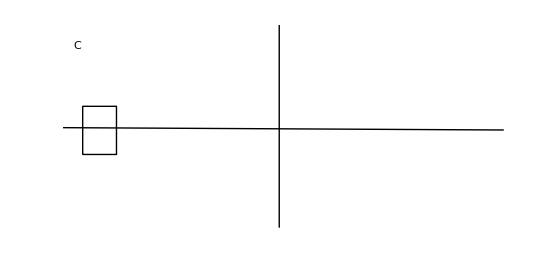
We’re now going to write this as a construction where there’s another braid at the far left which handles the connection:


-Graphics--Graphics-

```mathematica
<<IGraphM`
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
CellAdjacencyMatrix=IGMeshCellAdjacencyMatrix;
```

```mathematica
ClearAll[GeneralGoertiz];GeneralGoertiz[n_]:= Block[{B,BraidC,ys=4,xs=7,blen,flen,clen},
B = {1,-2,3,-2};
BraidC = {-3,-2,-1};
blen = 3*Length[B];
clen = 3*Length[BraidC];
flen = 3*Length[FlypeBraid[n]];
Join[
TranslateF[Braid[n,B],{-flen/2-blen-xs,0,0}],
TranslateF[Braid[n,BraidC],{-flen/2-blen-xs-clen,0,0}],
TranslateF[Braid[n,Reverse[-B]],{flen/2+xs,0,0}],
TranslateF[Braid[n,InverseFlypeBraid[n]],{-flen/2,ys+n,0}],
TranslateF[Braid[n,FlypeBraid[n]],{-flen/2,-ys-n,0}],
TranslateF[Stackers[n/2,ys+n/2,xs+1],{-flen/2-xs,n/2,0}],
TranslateF[Stackers[n/2,-ys-n/2,xs+1],{-flen/2-xs,0,0}],
TranslateF[Stackers[n/2,-ys-n/2,xs+1],{flen/2,n+ys,0}],
TranslateF[Stackers[n/2,ys+n/2,xs+1],{(+flen)/2,-ys-n/2,0}],
(*Now we connect the right hand side *)
Join[Table[
TranslateF[Wrapper[-blen-xs,-ys-n/2- 2i-1,0],{(+flen)/2+blen+xs+1,i+1,0}],
{i,0,(n/2)-1}],
Table[
TranslateF[Wrapper[-blen-xs,+ys+n/2+2i+1,0],{(+flen)/2+blen+xs+1,n-i,0}],
{i,0,(n/2)-1}],
(*Now we connect the left hand side*)
Table[
TranslateF[Wrapper[blen+xs+clen,-ys-n/2-2i-1,0],{-(+flen)/2-blen-xs-clen+1,i+1,0}],
{i,0,(n/2)-1}],
Table[
TranslateF[Wrapper[blen+xs+clen,+ys+n/2+2i+1,0],{-(+flen)/2-blen-xs-clen+1,n-i,0}],
{i,0,(n/2)-1}]
]]
]
```

```mathematica
DisplayBraid[GeneralGoertiz[4]]
```

-Graphics3D-

Now we have to take this entire thing and write it as a single strand. This is going to take two operations: Shatter and Glue. Shatter is going to take a list of vertices and write them as a MeshRegion, while Glue combines the MeshRegions, generates the corresponding graph, and finds a cycle. Interestingly, RegionUnion already seems to combine overlapping points.

```mathematica
Shatter[L_]:=DiscretizeRegion[Line[L],MaxCellMeasure->2]
```

```mathematica
Glue[L_]:= Block[{R,G},
R = RegionUnion[L];
G = IncidenceGraph[CellAdjacencyMatrix[R,0,1]];
Tube[Append[#,First[#]]&@MeshCoordinates[R][[(FindFundamentalCycles[G][[1]])[[All,1]]]],0.2]
]
```

```mathematica
Graphics3D[Glue[Shatter/@GeneralGoertiz[4]]]
```

-Graphics3D-

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/data/diagrams/hardgoeritz/4-strand-example-1.tsv",Glue[Shatter/@GeneralGoertiz[4]][[1]]]
```

/Users/jasoncantarella/KnotTools/data/diagrams/hardgoeritz/4-strand-example-1.tsv